```mathematica
readFile[file_String?FileExistsQ,n_Integer]:=Module[{str=OpenRead[file],data},Skip[str,String,n];
(*data=StringSplit[str,","];*)
data=ReadList[str,String,RecordLists->True];
Close[str];
StringTrim[#]&/@StringSplit[data[[All,1]],","]
];
data :=readFile["D:\\log.csv",1]
```

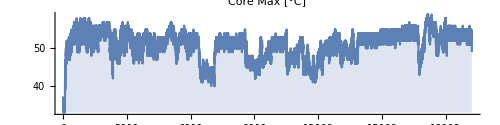
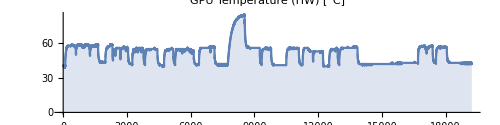

```mathematica
ListLinePlot[ToExpression/@data[[All,#id]], Filling->Bottom,AspectRatio->1/4,ImageSize->500,PlotLabel->#name]&/@{<|"name"->"Core Max [°C]","id"->27|>,<|"name"->"GPU Temperature (HW) [°C]","id"->49|>}
```

```mathematica
lm=LinearModelFit[Sort@Table[{data[[x,8]],data[[x,9]]},{x,1,Length[data]}],a,a];r2=lm["RSquared"];
Show[Plot[lm[x],{x,0,7}],ListPlot[pts],AxesOrigin->{0,0},PlotRange->{{0,7},{0,5}},PlotLabel->"The correlation is "<>If[D[lm["BestFit"],a]<0,"negative","positive"],Epilog->Inset[Style["\!\(\*SuperscriptBox[\"R\", \"2\"]\) = "<>ToString[r2],11],{1.5,4.5}]]
```